Video - igre skozi čas
Analiza videoiger glede na različne lastnosti.

## Pridobivanje podatkov

Podatke sem pridobil iz podatkovne baze Wolfram data repository.

```mathematica
podatki= ResourceData["Video Games Until April 2017"]
```

Dataset[<>]

## Analiza iger glede na žanr, popularnost in oceno

Analiziral bom in narisal nekaj grafov glede na žanr, popularnost ter oceno. Podatki so obdelani in predstavljeni tudi z grafi.

```mathematica
shooters = Length[Select[podatki, MemberQ[#["Genres"], "Shooter"]&]]
```

3108

```mathematica
advent = Length[Select[podatki, MemberQ[#["Genres"], "Adventure"]&]]
```

4661

```mathematica
indie = Length[Select[podatki, MemberQ[#["Genres"], "Indie"]&]]
```

3164

```mathematica
platform = Length[Select[podatki, MemberQ[#["Genres"], "Platform"]&]]
```

1993

```mathematica
sport = Length[Select[podatki, MemberQ[#["Genres"], "Sport"]&]]
```

1507

```mathematica
rpg = Length[Select[podatki, MemberQ[#["Genres"], "Role-playing (RPG)"]&]]
```

2667

```mathematica
PieChart[<|"Shooters"->shooters,"Adventure"->advent,"Indie"->indie,"Platform"->platform, "Sport"-> sport, "RPG" -> rpg|>,ChartLabels->Callout[Automatic], PlotLabel->"Popularnost najpogostejših žanrov"]
```

-Graphics-

```mathematica
popularnost = podatki[All, "Popularity"]
```

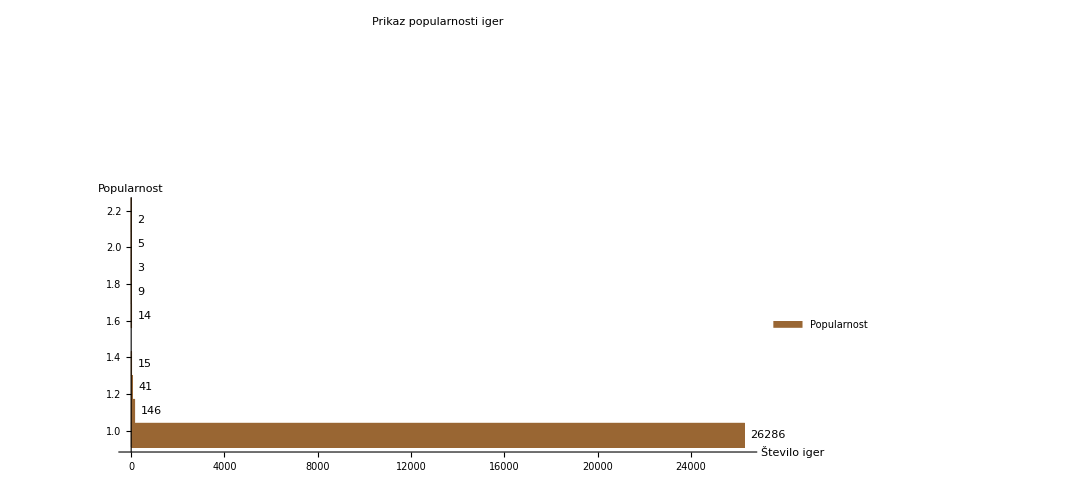

```mathematica
Histogram[popularnost,ChartStyle->Brown, BarOrigin->Left,LabelingFunction->After,ImageSize->{800,550},ChartLegends->{"Popularnost"},PlotLabel->"Prikaz popularnosti iger",AxesLabel->{"Število iger","Popularnost"}]
```

```mathematica
ocene = podatki[All, "Rating"]
```

Dataset[<>]

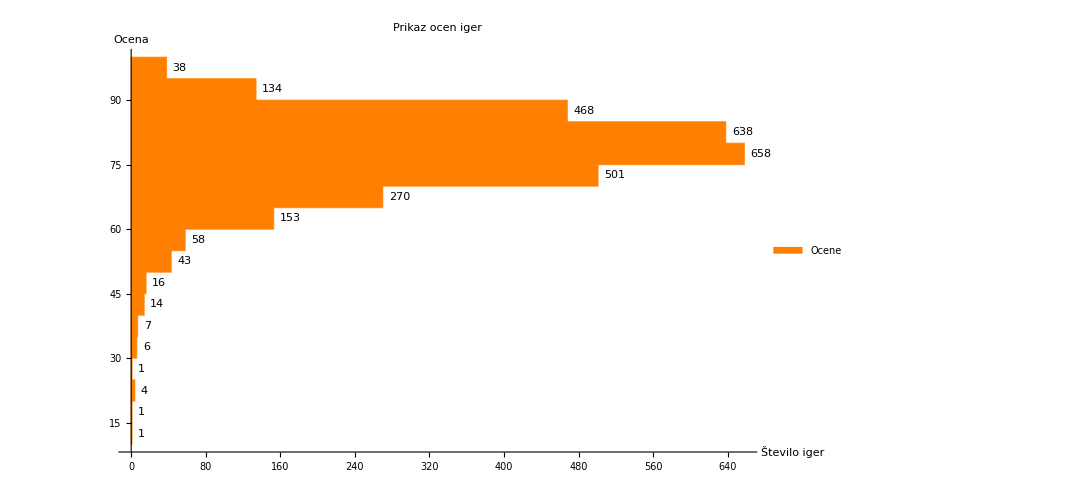

```mathematica
Histogram[ocene,ChartStyle -> Orange, BarOrigin->Left,LabelingFunction->After,ImageSize->{800,550},ChartLegends->{"Ocene"},PlotLabel->"Prikaz ocen iger",AxesLabel->{"Število iger","Ocena"}]
```

Graf popularnosti proti oceni nam kaže, da nerabijo igre biti dobre da so popularne saj je veliko več iger z dobro oceno, kot jih je popularnih.

## Analiza glede na čas

Analizirali bomo večjih korporaciji in koliko iger producirajo na leto.

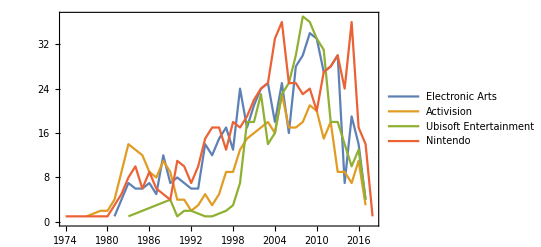

```mathematica
Table[Legended[Normal@GroupBy[Select[podatki,MemberQ[#Publishers,p]&&!MissingQ@#@"FirstReleaseDate"&],Normal@DateObject[#@"FirstReleaseDate","Year"]&,Length],p],{p,{"Electronic Arts","Activision","Ubisoft Entertainment", "Nintendo"}}]//DateListPlot
```

## Analiza posameznih serij iger

Poglejmo si za primer kako so se spreminjale ocene Super Mariota skozi čas in kakšno bi bilo povprečje njihovih ocen (regresiska premica)

```mathematica
superMario=Select[podatki,#Collection=="Super Mario"&]
sm1 = superMario[All, {"Rating", "FirstReleaseDate"}];
sm2 = sm1[Select[#Rating > 0 &]];
sm3 = {};
sm4={};
Do[
]
```

## Aplikacija v oblaku

```mathematica
IskanaIgra[zanr_] := Select[]
```